```mathematica
ClearAll["Global`*"]
<<Utilities`CleanSlate`
CleanSlate[]
ClearInOut[]

pdConv[f_]:=TraditionalForm[f/.Derivative[inds__][g_][vars__]:>Apply[Defer[D[g[vars],##]]&,Transpose[{{vars},{inds}}]/.{{var_,0}:>Sequence[],{var_,1}:>{var}}]]

Needs["VariationalMethods`"]
```

(CleanSlate) Contexts purged: {Global`}

(CleanSlate) Approximate kernel memory recovered: 255 Kb

{Utilities`CleanSlate`,CompiledFunctionTools`,IPOPTLink`,VariationalMethods`,DocumentationSearch`,ResourceLocator`,System`,Global`}

```mathematica
Clear[r]
r = { b Sin[ Ω t + ϕ ] + L Sin[θ[t]] , b Cos[ Ω t + ϕ ] + L Cos[ θ[t] ]  }
```

{b Sin[ϕ+t Ω]+L Sin[θ[t]],b Cos[ϕ+t Ω]+L Cos[θ[t]]}

```mathematica
D[r, t]
```

{b Ω Cos[ϕ+t Ω]+L Cos[θ[t]] θ'[t],-b Ω Sin[ϕ+t Ω]-L Sin[θ[t]] θ'[t]}

```mathematica
D[r, t] . D[r, t]
```

(b Ω Cos[ϕ+t Ω]+L Cos[θ[t]] θ'[t])^2+(-b Ω Sin[ϕ+t Ω]-L Sin[θ[t]] θ'[t])^2

```mathematica
D[r, t] . D[r, t]  // Expand
```

b^2 Ω^2 Cos[ϕ+t Ω]^2+b^2 Ω^2 Sin[ϕ+t Ω]^2+2 b L Ω Cos[ϕ+t Ω] Cos[θ[t]] θ'[t]+2 b L Ω Sin[ϕ+t Ω] Sin[θ[t]] θ'[t]+L^2 Cos[θ[t]]^2 θ'[t]^2+L^2 Sin[θ[t]]^2 θ'[t]^2

```mathematica
D[r, t] . D[r, t]  // Expand  // Simplify
```

b^2 Ω^2+2 b L Ω Cos[ϕ+t Ω-θ[t]] θ'[t]+L^2 θ'[t]^2

```mathematica
Clear[T]
T = 1/2 m ( D[r, t] . D[r, t]  // Expand  // Simplify  )
```

1/2 m (b^2 Ω^2+2 b L Ω Cos[ϕ+t Ω-θ[t]] θ'[t]+L^2 θ'[t]^2)

```mathematica
r
r[[2]]
```

{b Sin[ϕ+t Ω]+L Sin[θ[t]],b Cos[ϕ+t Ω]+L Cos[θ[t]]}

b Cos[ϕ+t Ω]+L Cos[θ[t]]

```mathematica
Clear[V]
V = m g r[[2]]
```

g m (b Cos[ϕ+t Ω]+L Cos[θ[t]])

```mathematica
Clear[ℒ]
ℒ = T - V
```

-g m (b Cos[ϕ+t Ω]+L Cos[θ[t]])+1/2 m (b^2 Ω^2+2 b L Ω Cos[ϕ+t Ω-θ[t]] θ'[t]+L^2 θ'[t]^2)

```mathematica
Clear[q]
q = { θ[t] }
```

{θ[t]}

```mathematica
D[ D[ ℒ , D[q[[1]], t] ], t ]  - D[ ℒ , q[[1]] ]  == 0  // Expand  // Simplify
```

L m (-b Ω^2 Sin[ϕ+t Ω-θ[t]]-g Sin[θ[t]]+L θ''[t])==0

```mathematica
Clear[eqs]
eqs = 
EulerEquations[ ℒ , q , t ] ;
eqs // TableForm
```

L m (b Ω^2 Sin[ϕ+t Ω-θ[t]]+g Sin[θ[t]]-L θ''[t])==0

```mathematica
Clear[parameters]
parameters = { 
L -> 2 , 
b-> 1 , 
g -> 9.8 , 
Ω -> 2 ,
ϕ-> 0 ,  
m -> 0.5 
} ;
parameters // TableForm
```

L→2
b→1
g→9.8
Ω→2
ϕ→0
m→0.5

```mathematica
eqs /. parameters // Expand
```

{4. Sin[2 t-θ[t]]+9.8 Sin[θ[t]]-2. θ''[t]==0}

```mathematica
Clear[ics]
ics = { 
θ[0] == π/4 ,
θ'[0] == 0 
} ;
ics // TableForm
```

θ[0]==π/4
θ'[0]==0

```mathematica
Clear[solution]
solution[t_] = 
First[ NDSolve[ Union[ eqs /. parameters , ics ] , q , { t, 0, 300 } ] ]
```

{θ[t]→InterpolatingFunction[…][t]}

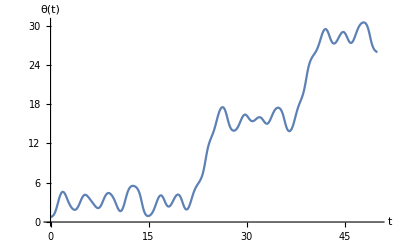

```mathematica
Plot[ Evaluate[ q /. solution[t] ] , { t, 0, 50 } , AxesLabel -> { t , q[[1]] }  ]
```

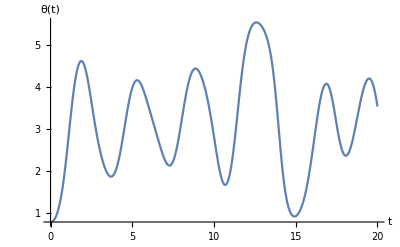

```mathematica
Plot[ q /. solution[t] , { t, 0, 20 } , AxesLabel -> { t , q[[1]] } ]
```

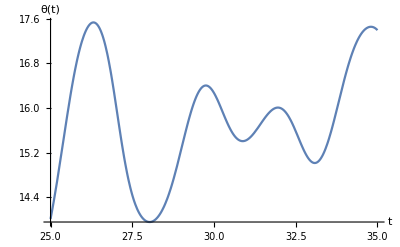

```mathematica
Plot[ q /. solution[t] , { t, 25, 35 }, AxesLabel -> { t , q[[1]] }  ]
```

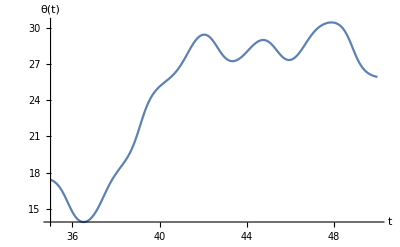

```mathematica
Plot[ q /. solution[t] , { t, 35, 50 } , AxesLabel -> { t , q[[1]] } ]
```

```mathematica
Animate[ 
ParametricPlot[ { solution[t][[1,2]] , solution'[t][[1,2]] } , { t , 0, tmax } , AxesLabel-> { q[[1]] , D[q[[1]], t] } ]  ,
{ tmax , 1 , 75 , 0.5  } ]
```